## Homework 3

## 4. Joukowski Transform

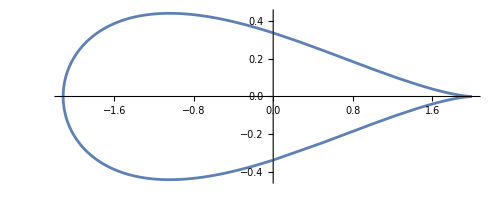

```mathematica
(*Define the Joukowski transform*)
joukowskiTransform[z_]:=z+1/z

(*Parametrize the circle in the z-plane*)
r=6/5;
center=-1/5;
z[θ_]:=r*Exp[I*θ]+center

(*Apply the Joukowski transform to the circle parametrization*)
w[θ_]:=joukowskiTransform[z[θ]]

(*Plot the image of the circle under the Joukowski transform*)
p1=ParametricPlot[{Re[w[θ]],Im[w[θ]]},{θ,0,2*Pi},AspectRatio->Automatic]
```

The potential flow around a cylinder (circle in the z - plane) with circulation Γ and far-field velocity U is given by the complex potential Φ(z)=U(z+1/z)+(i Γ)/(2 π)Log(z). For the simplest case, we choose Φ(z)=z+1/z+i Log(z)

First, solve for z given w by inverting w=z+1/z​ to get z(w) =1/2 (w+√(-4+w^2)) for one branch.

```mathematica
Clear[w,Φ]
Reduce[z+1/z==w,{z}]
```

z==1/2 (w-√(-4+w^2))||z==1/2 (w+√(-4+w^2))

Then, Substitute z (w) into Φ(z) to get Φ (w) .

```mathematica
Φz := z+1/z+I Log[z]/.{z->6/5(z-1/5)}
```

Stream Plot

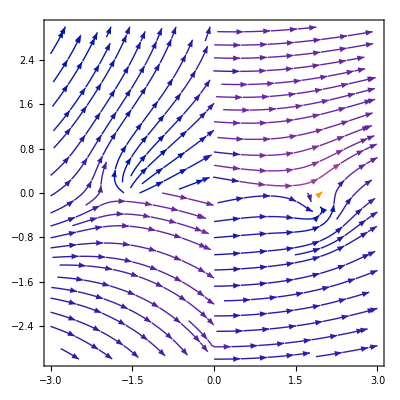

```mathematica
(*Define the potential function Φ(z)*)U=1; (*Far away velocity*)
Γ=1; (*Circulation-You can adjust this as needed*)
Φ[w_]:=Φz /.{z->1/2(w+√(w^2-4) )}//Simplify

(*Calculate the velocity field V(z)*)
V[w_]:=D[Φ[z],z]/.{z->w}

(*To use StreamPlot,we need the real and imaginary parts of the velocity field*)
velocityField[w_]:=Through[{Re,Im}[V[w]]]

(*Plot the streamlines in the w-plane*)
p2=StreamPlot[velocityField[x+I y],{x,-3,3},{y,-3,3},AspectRatio->Automatic]
```

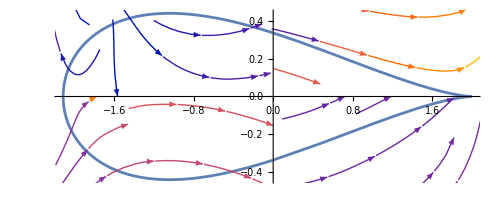

```mathematica
Show[p1,p2]
```